不同的三相输入对DQ分量的影响

1、三相静止坐标系ABC

三相电压如下

```mathematica
U =220;
Uma=Sqrt[2]*300;
Umb=Sqrt[2]*220;
Umc=Sqrt[2]*50;
ua1=Uma*Cos[wt];
ub1=Umb*Cos[wt-120*Pi/180];
uc1=Umc*Cos[wt+120*Pi/180];
```

3次谐波

```mathematica
Uh3=Sqrt[2]*50;
ua3=Uh3*Cos[3*wt];
ub3=Uh3*Cos[3*(wt-120*Pi/180)];
uc3=Uh3*Cos[3*(wt+120*Pi/180)];
```

5次谐波

```mathematica
Uh5=Sqrt[2]*50;
ua5=Uh5*Cos[5*wt];
ub5=Uh5*Cos[5*(wt-120*Pi/180)];
uc5=Uh5*Cos[5*(wt+120*Pi/180)];
```

7次谐波

```mathematica
Uh7=Sqrt[2]*50;
ua7=Uh7*Cos[7*wt];
ub7=Uh7*Cos[7*(wt-120*Pi/180)];
uc7=Uh7*Cos[7*(wt+120*Pi/180)];
```

实际三相电压

```mathematica
ua=ua1;
ub=ub1;
uc=uc1;
uab=ua-ub;
ubc=ub-uc;
uca=uc-ua;
```

三相相电压波形如下

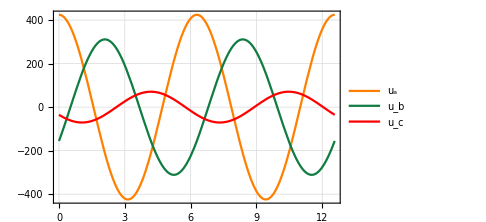

```mathematica
Plot[{ua,ub,uc},{wt,0,4*Pi},Frame->True,GridLines->Automatic,PlotLegends->LineLegend[{"u_a","u_b","u_c"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->5],PlotStyle->{Orange,{RGBColor["#107c41"]},Red},ImageSize->Medium]
```

三相线电压波形如下

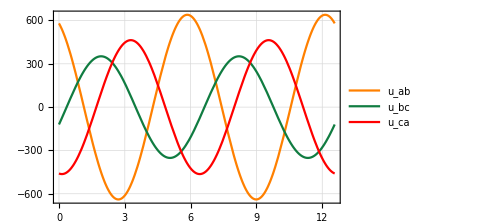

```mathematica
Plot[{uab,ubc,uca},{wt,0,4*Pi},Frame->True,GridLines->Automatic,PlotLegends->LineLegend[{"u_ab","u_bc","u_ca"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->5],PlotStyle->{Orange,{RGBColor["#107c41"]},Red},ImageSize->Medium]
```

三相相电压矩阵表示

```mathematica
ABC={{ua},{ub},{uc}};
MatrixForm[ABC]
```

(300 √2 Cos[wt]
-220 √2 Sin[π/6-wt]
-50 √2 Sin[π/6+wt])

## 2、三相静止坐标系ABC-两相静止坐标系αβ

Clark变换就是三相静止坐标系ABC到两相静止坐标系αβ的变换

-Graphics-

Clark变换有等功率变换和等幅值变换，二者只是系数不同，以下是等幅值变换
 [α
β]=2/3[1 | -1/2 | -1/2
0 | (√3)/2 | -(√3)/2][a
b
c]

```mathematica
ABC2AB=2/3*{{1,-1/2,-1/2},{0,Sqrt[3]/2,-Sqrt[3]/2}};
MatrixForm[ABC2AB]
```

(2/3 | -1/3 | -1/3
0 | 1/(√3) | -1/(√3))

通过Clark变换从ABC坐标系变换到αβ坐标系

```mathematica
AB=ABC2AB.ABC;
MatrixForm[AB]
```

(200 √2 Cos[wt]+220/3 √2 Sin[π/6-wt]+50/3 √2 Sin[π/6+wt]
-220 √(2/3) Sin[π/6-wt]+50 √(2/3) Sin[π/6+wt])

αβ波形如下

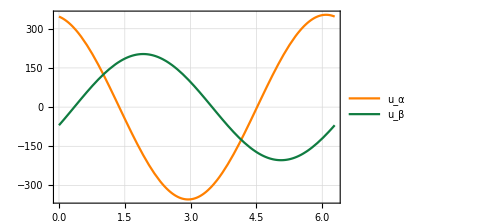

```mathematica
ualpha=AB[[1,1]];
ubeta=AB[[2,1]];
Plot[{ualpha,ubeta},{wt,0,2*Pi},Frame->True,GridLines->Automatic,PlotLegends->LineLegend[{"u_α","u_β"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->5],PlotStyle->{Orange,{RGBColor["#107c41"]}},ImageSize->Medium]
```

## 3、两相静止坐标系αβ-两相旋转坐标系dq

两相静止坐标系αβ到两相旋转坐标系的变换，φ是d轴和α轴之间的夹角

-Graphics-

变换如下
                           [d
q]=[cosφ | sinφ
-sinφ | cosφ][α
β]

```mathematica
AB2DQ={{Cos[wt],Sin[wt]},{-Sin[wt],Cos[wt]}};
MatrixForm[AB2DQ]
```

(Cos[wt] | Sin[wt]
-Sin[wt] | Cos[wt])

DQ变换后的DQ分量波形

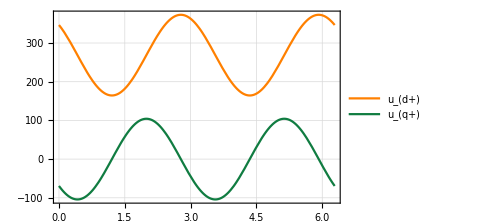

```mathematica
DQ=AB2DQ.AB;
ud=DQ[[1,1]];
uq=DQ[[2,1]];
Plot[{ud,uq},{wt,0,2*Pi},Frame->True,GridLines->Automatic,PlotLegends->LineLegend[{"u_(d+)","u_(q+)"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->5],PlotStyle->{Orange,{RGBColor["#107c41"]}},ImageSize->Medium]
```

4、三相静止坐标系ABC到两相旋转坐标系dq的变换

三相静止坐标系ABC变换到两相旋转坐标系，即Park变换
[d
q]=2/3[cosφ | -1/2cosφ+(√3)/2 sinφ | -1/2cosφ-(√3)/2 sinφ
-sinφ | 1/2 sinφ+(√3)/2 cosφ | 1/2 sinφ-(√3)/2 cosφ][a
b
c]=√(2/3)[cosφ | cos(φ-(2π)/3) | cos(φ+(2π)/3)
-sinφ | -sin(φ-(2π)/3) | -sin(φ+(2π)/3)][a
b
c]

```mathematica
ABC2DQZ=2/3 {{Cos[wt], -1/2 Cos[wt]+Sqrt[3]/2 Sin[wt], -1/2Cos[wt]-Sqrt[3]/2 Sin[wt]},{-Sin[wt], 1/2 Sin[wt]+Sqrt[3]/2 Cos[wt], 1/2 Sin[wt]-Sqrt[3]/2 Cos[wt]},{1/2, 1/2, 1/2}};
MatrixForm[ABC2DQZ]
```

((2 Cos[wt])/3 | 2/3 (-Cos[wt]/2+1/2 √3 Sin[wt]) | 2/3 (-Cos[wt]/2-1/2 √3 Sin[wt])
-(2 Sin[wt])/3 | 2/3 (1/2 √3 Cos[wt]+Sin[wt]/2) | 2/3 (-1/2 √3 Cos[wt]+Sin[wt]/2)
1/3 | 1/3 | 1/3)

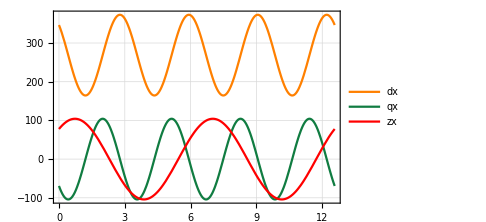

```mathematica
DQZ=ABC2DQZ.ABC;
dx=DQZ[[1,1]];
qx=DQZ[[2,1]];
zx=DQZ[[3,1]];
Plot[{dx,qx,zx},{wt,0,4*Pi},Frame->True,GridLines->Automatic,PlotLegends->LineLegend["Expressions",LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->5],PlotStyle->{Orange,{RGBColor["#107c41"]},Red},ImageSize->Medium]
```